```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\cheby\LPA\v2\phase\T25\smallstep

```mathematica
alist=Table[Flatten[Import["./exam/buffer/a.dat"]],{i,1,1}];
alist1=Table[Rest[alist[[i]]],{i,1,1}];
```

```mathematica
ρmin=0;
ρmax=9000;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
```

```mathematica
rhoend=250;
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/191}];
Vall=Table[Table[Evaluate[(test=SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alist[[i]]],52])],{ρ,0,rhoend,rhoend/191}],{i,1,1}];
Vdata=Table[Transpose[{sigma,Vall[[i]]-Vall[[i]][[1]]+10^7}],{i,1,1}];
```

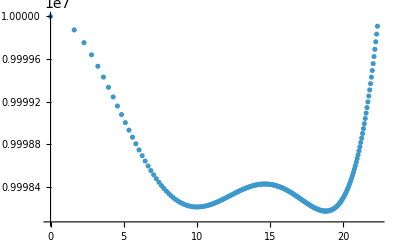

```mathematica
ListPlot[Vdata,PlotRange->{All,All},ScalingFunctions->{Automatic,Automatic}]
```